```mathematica
μ=Quantity[1370/2,"Megaelectronvolts"]/Quantity["SpeedOfLight"]^2;
```

```mathematica
α=Rationalize[0.38];
```

```mathematica
a=Rationalize[2.43*10^(-3)]/Quantity["Megaelectronvolts"];
```

```mathematica
8*μ*α*Quantity["SpeedOfLight"]/(3*Quantity["ReducedPlanckConstant"])*Quantity["Meters"]
```

(7414161383648000000000000000000 π)/6621486190496429

```mathematica
N[%]
```

3.51768×10^15

```mathematica
CubeRoot[2*μ/(Quantity["ReducedPlanckConstant"]^3*Quantity["SpeedOfLight"]*a^2)]*Quantity["Meters"]
```

(3560392520000000000000000000000 10^(2/3) (137/3)^(1/3) π)/59593375714467861

```mathematica
N[%]
```

3.11398×10^15

```mathematica
b=Quantity[Rationalize[10^(-15)],"Meters"];
```

```mathematica
E0=Quantity["ReducedPlanckConstant"]^2/(2*μ*b^2)/Quantity["Megaelectronvolts"]
```

43844079370934911635877461752041/(156299949073499148432000000000 π^2)

```mathematica
N[E0]
```

28.4219

```mathematica
N[E0,30]
```

28.4218519833473994252300447491

```mathematica
β=8*b*μ*α*Quantity["SpeedOfLight"]/(3*Quantity["ReducedPlanckConstant"])
```

(7414161383648000 π)/6621486190496429

```mathematica
N[β,30]
```

3.51768081444135951932841186128

```mathematica
γ=2*μ*b^3/(Quantity["ReducedPlanckConstant"]^3*Quantity["SpeedOfLight"]*a^2)
```

(618321299508519220337402809600000000000000000000000 π^3)/634914456838118956576076623304100900125006093995143

```mathematica
N[γ,30]
```

30.1959438525934070224310663778

```mathematica
CubeRoot[2*μ/(Quantity["ReducedPlanckConstant"]^3*Quantity["SpeedOfLight"]*a^2)*Quantity[10^(-15),"Meters"]^3]
```

(3560392520000000 10^(2/3) (137/3)^(1/3) π)/59593375714467861

```mathematica
%^3
```

(618321299508519220337402809600000000000000000000000 π^3)/634914456838118956576076623304100900125006093995143

```mathematica
Assuming[{p>0,q>0,k>0,x>0},Solve[p*x^3+1==k*x,{x}]]//FullSimplify
```

{{x→((-9 p^2+√3 √(p^3 (-4 k^3+27 p)))^(1/3) (2^(1/3)/p+(2 3^(1/3) k)/((-9 p^2+√3 √(p^3 (-4 k^3+27 p)))^(2/3))))/6^(2/3)},{x→((-1)^(1/3) (-9 p^2+√3 √(p^3 (-4 k^3+27 p)))^(1/3) ((-2)^(1/3)/p-(2 3^(1/3) k)/((-9 p^2+√3 √(p^3 (-4 k^3+27 p)))^(2/3))))/6^(2/3)},{x→(-(-3 ⅈ+√3) k p+(-9 p^2+√3 √(p^3 (-4 k^3+27 p)))^(2/3) Root-0.757-1.31 ⅈRoot[-12+#1^6&,3]-0.7565428747114508)/(2^(2/3) 3^(5/6) p (-9 p^2+√3 √(p^3 (-4 k^3+27 p)))^(1/3))}}

```mathematica
Solve[-β/x^2+γ+4/x^3==0,{x}]
```

{{x→(Root-1.84Root[634914456838118956576076623304100900125006093995143-177730426084906788406142002304957980245157979304000 #1+154580324877129805084350702400000000000000000000000 #1^3&,1]-1.839266852104165)/π},{x→(Root0.920-1.18 ⅈRoot[634914456838118956576076623304100900125006093995143-177730426084906788406142002304957980245157979304000 #1+154580324877129805084350702400000000000000000000000 #1^3&,2]0.9196334260520825)/π},{x→(Root0.920+1.18 ⅈRoot[634914456838118956576076623304100900125006093995143-177730426084906788406142002304957980245157979304000 #1+154580324877129805084350702400000000000000000000000 #1^3&,3]0.9196334260520825)/π}}

```mathematica
N[%]
```

{{x→-0.585457},{x→0.292728-0.374933 ⅈ},{x→0.292728+0.374933 ⅈ}}

```mathematica
N[Solve[(D[ϵ+β/x-γ*x-l(l+1)/x^2,x]==0)/.l->1,{x}][[1]],30]
```

{x→0.434238646090311696003693054554}

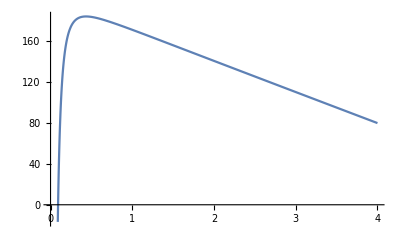

```mathematica
Plot[ϵ+β/x-γ*x-l(l+1)/x^2/.{ϵ->200,l->1},{x,0,4}]
```

```mathematica
N[Solve[(ϵ+β/x-γ*x-l(l+1)/x^2==0)/.{l->1,ϵ->16},{x}],30]
```

{{x→-0.348746616933074737441669428013},{x→0.383878639035916880278567779957},{x→0.49474046931874410308381703089}}

```mathematica
N[Solve[(ϵ+β/x-γ*x-l(l+1)/x^2==0)/.{l->1,x->0.434238646090311696003693054554},ϵ],30]
```

{{ϵ→15.617968214669834906912012772}}

```mathematica
N[Solve[(ϵ+β/x-γ*x-l(l+1)/x^2==0)/.{l->0,ϵ->16},{x}],30]
```

{{x→-0.167135921715786333370007581758},{x→0.697008413137372579290722964592}}

```mathematica
NIntegrate[Sqrt[(ϵ+β/x-γ*x-l(l+1)/x^2)/.{l->0,ϵ->16}],{x,0,0.697008413137372579290722964592}]
```

3.4119

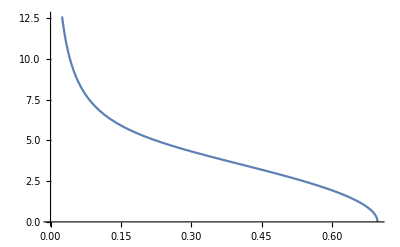

```mathematica
Plot[Sqrt[(ϵ+β/x-γ*x-l(l+1)/x^2)/.{l->0,ϵ->16}],{x,0,0.697008413137372579290722964592}]
```

```mathematica
Vals = {l->0,ϵ->6};
sol=NSolve[(ϵ+β/x-γ*x-l(l+1)/x^2==0)/.Vals,{x}]
upper=Max[x/.sol]
NIntegrate[Sqrt[(ϵ+β/x-γ*x-l(l+1)/x^2)/.Vals],{x,0,upper}]-(3/4)*Pi
```

{{x→0.454831},{x→-0.256129}}

0.454831

0.00563765